```mathematica
ClearAll["Global`*"]
$RecursionLimit=1000000
d2[n_,k_]:=d2[n,k]=Sum[d2[j,k-1] d2[n/j,1],{j,Divisors[n]}];d2[n_,1]:=1;d2[1,1]:=0;d2[n_,0]:=0;d2[1,0]:=1
D2[n_,k_]:=D2[n,k]=D2[n-1,k]+d2[n,k];D2[1,k_]:=0; D2[n_,0]:=1
K[n_]:=K[n]=FullSimplify[MangoldtLambda[n]/Log[n]]
k2[n_,k_]:=k2[n,k]=Sum[k2[j,k-1] k2[n/j,1],{j,Divisors[n]}];k2[n_,1]:=K[n];k2[1,1]:=0;k2[n_,0]:=0;k2[1,0]:=1
K2[n_,k_]:=K2[n,k]=K2[n-1,k]+k2[n,k];K2[1,k_]:=0; K2[n_,0]:=1
e2[n_,1]:=e2[n,1]=Sum[  1/(k!) d2[n,k],{k,0,Log[2,n]}];e2[1,1]:=0;
e2[n_,k_]:=Sum[e2[j,k-1]e2[n/j,1],{j,Divisors[n]}];e2[n_,0]:=0;e2[1,0]:=1
E2[n_,k_] := E2[n,k] = E2[n-1,k]+e2[n,k];E2[1,k_]:=0; E2[n_,0]:=1
E1[n_,k_] := Sum[ Binomial[k,j] E2[n,j],{j,0,Log[2,n]}]
K1[n_,k_] := Sum[ Binomial[k,j] K2[n,j],{j,0,Log[2,n]}]
D1[n_,k_] := Sum[ Binomial[k,j] D2[n,j],{j,0,Log[2,n]}]
```

1000000

```mathematica
E1[100,1]
```

218593/720

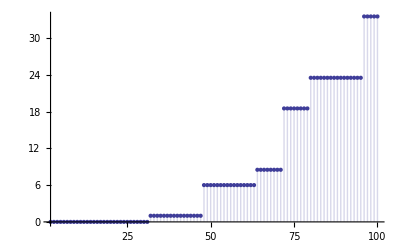

```mathematica
DiscretePlot[ K2[n,5],{n,2,100}]
```

```mathematica
KD2[n_,k_] := Sum[ k^j/j! K2[n,j],{j,0,Log[2,n]}]
KD1[n_,k_] := Sum[ k^j/j! K1[n,j],{j,0,Log[2,n]*3}]
DE2[n_,k_] := Sum[ k^j/j! D2[n,j],{j,0,Log[2,n]}]
DE1[n_,k_] := Sum[ k^j/j! D1[n,j],{j,0,Log[2,n]*3}]
```

```mathematica
N[KD2[1000,3I]]
```

4101.65-2109.86 ⅈ

```mathematica
D1[1000,2I]
```

14149/84-(736109 ⅈ)/567

```mathematica
N[KD1[1000,ss=3I]/(E^ss)]
```

4101.65-2109.86 ⅈ

```mathematica
N[KD1[2,1]]
```

5.16667

```mathematica
K1[1,0]
```

0

```mathematica
N[DE2[100,2]]
```

1333.89

```mathematica
N[E1[100,2]]
```

1333.89

```mathematica
N[DE1[100,ss=2]/E^ss]
```

1333.89

```mathematica
Dhyp[n_,k_,a_]:=Sum[ d2[m,2]^(k-j) Binomial[k,j] Dhyp[n/(m^(k-j)),j,m+1],{m,a,n^(1/k)},{j,0,k-1}]
Dhyp[n_,1,a_]:=Floor[n]-a+1;Dhyp[n_,0,a_]:=1
```

```mathematica
Dhyp[100,2,2]
```

116

```mathematica
D2[100,8]
```

0

```mathematica
CoefficientList[Series[Cos[x],{x,0,30}],x]
```

```mathematica
cc:=cc={1,0,-1/2,0,1/24,0,-1/720,0,1/40320,0,-1/3628800,0,1/479001600,0,-1/87178291200,0,1/20922789888000,0,-1/6402373705728000,0,1/2432902008176640000,0,-1/1124000727777607680000,0,1/620448401733239439360000,0,-1/403291461126605635584000000,0,1/304888344611713860501504000000,0,-1/265252859812191058636308480000000}
```

```mathematica
cc[[3]]
```

-1/2

```mathematica
CS2[n_,k_] := Sum[ cc[[j+1]] D2[n,j],{j,0,Log[2,n]}]
CS1[n_,k_] := Sum[ cc[[j+1]] D1[n,j],{j,0,Log[2,n]*3}]
```

```mathematica
N[CS2[20,1]]
```

-12.4583

```mathematica
N[CS1[20,1]]
```

-20.896

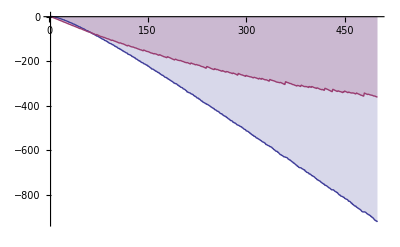

```mathematica
DiscretePlot[{CS2[n,1],CS1[n,1]},{n,2,500}]
```